```mathematica
sumIntDigits[n_, b_]:=Total[IntegerDigits[n, b]]
twistExpSumList[n_, b_, p_, q_] := Prepend[Accumulate[(Exp[2.0*Pi*I*(sumIntDigits[#, b]/p + (#/q))]&/@Range[n])], 0]
twistVisualizer[n_, b_, p_, q_]:=ListLinePlot[ReIm /@ twistExpSumList[n,b, p, q], PlotStyle->Thick]
expSumList[n_ ,b_, p_]:=Prepend[Accumulate[Exp[2.0*Pi*I*sumIntDigits[#, b]/p]&/@Range[n]], 0]
visualizer[n_, b_, p_]:=ListLinePlot[ReIm /@ expSumList[n,b, p], PlotStyle->Thick]
chunkVisualizer[n1_, n2_, b_, p_, c_]:=ListLinePlot[ReIm /@ Take[expSumList[n2,b, p], {n1, n2+1}], PlotStyle->{Thick, c}]
pointVisualizer[n_, b_, p_]:=ListPlot[ReIm /@ expSumList[n,b, p], PlotStyle->{PointSize[Large], Red}]
```

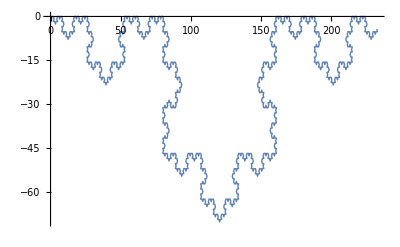

```mathematica
twistVisualizer[1000, 2, 2, 3]
```

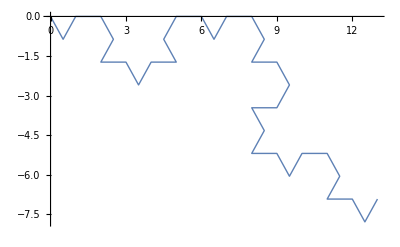
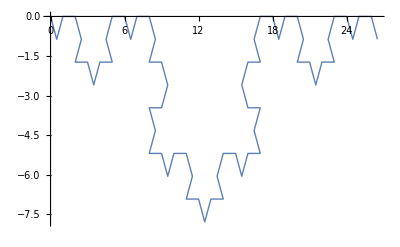
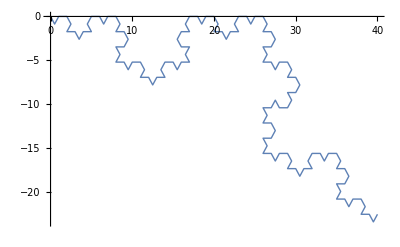
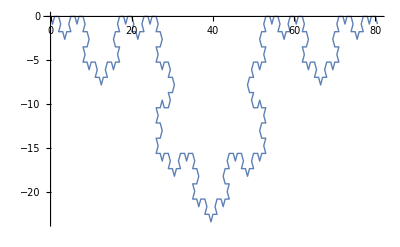
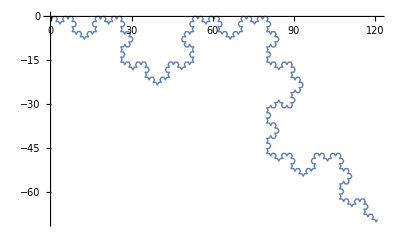
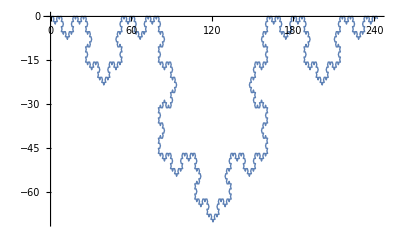
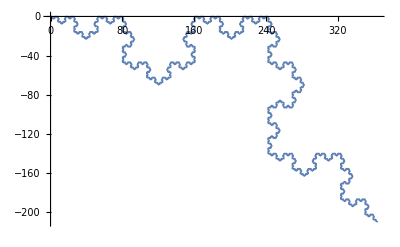
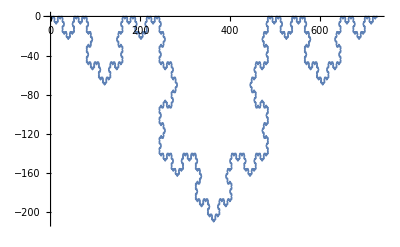

```mathematica
Table[twistVisualizer[2^k, 2, 2, 3], {k, 5, 15}]
```

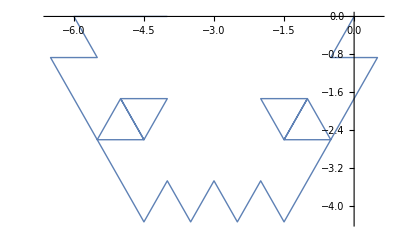
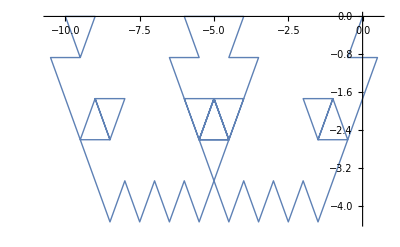
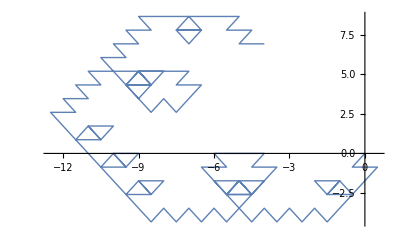
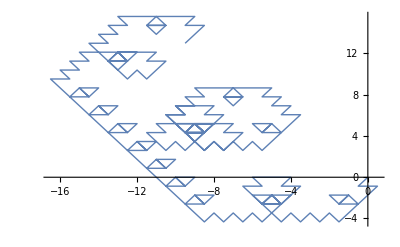
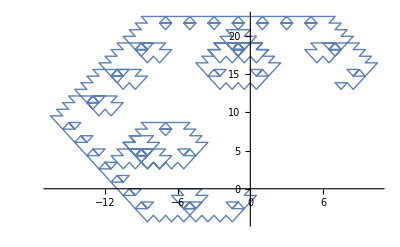
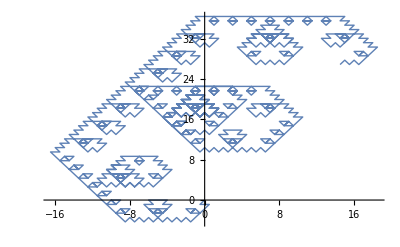
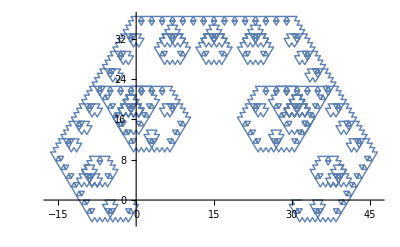
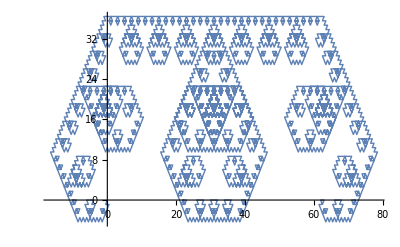

```mathematica
Table[twistVisualizer[2^k, 2, 3, 3], {k, 5, 15}]
```

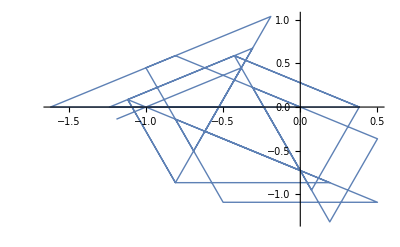
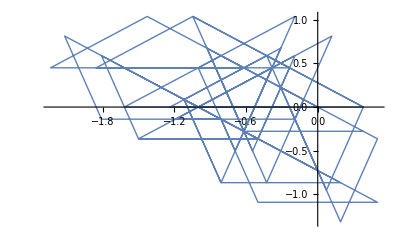
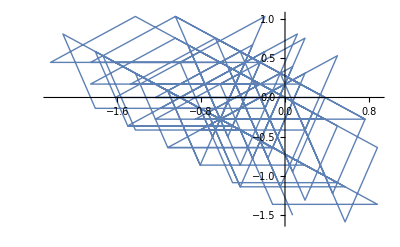
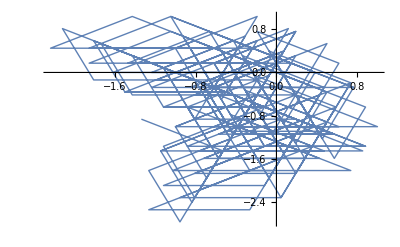
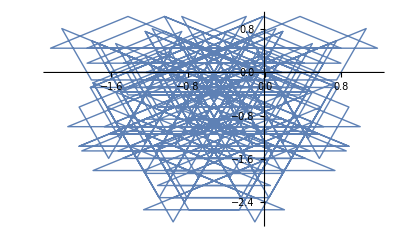
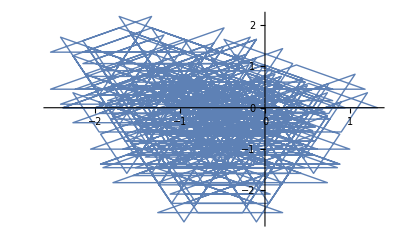
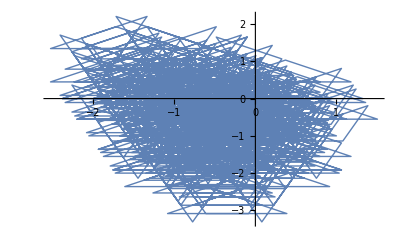
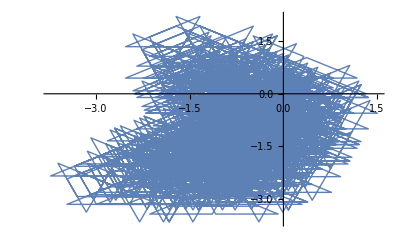

```mathematica
Table[twistVisualizer[2^k, 2, 5, 5], {k, 5, 15}]
```

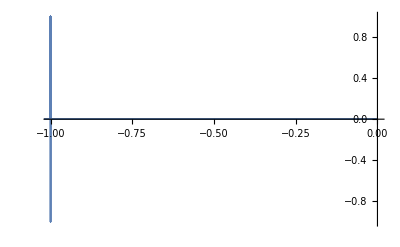
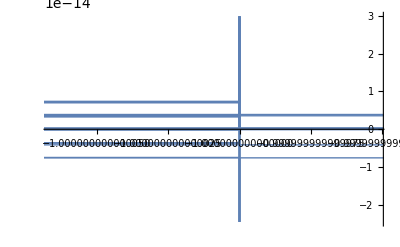
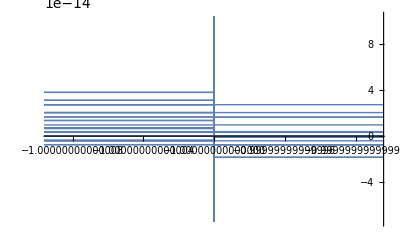
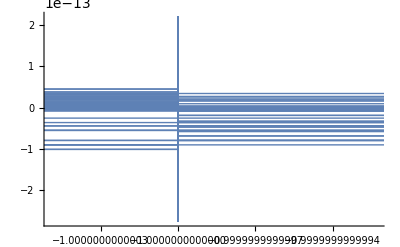
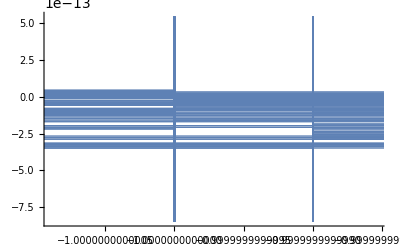
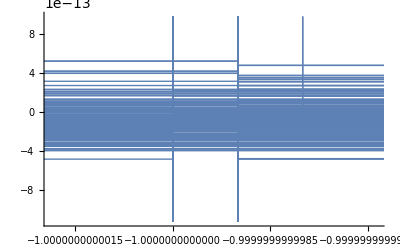
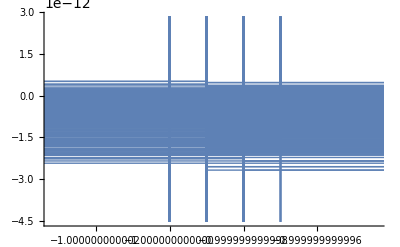
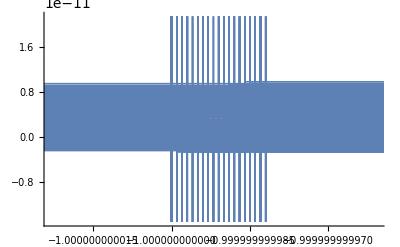
{{{{32,3},-Graphics-},{{64,3},-Graphics-},{{128,3},-Graphics-},{{256,3},-Graphics-},{{512,3},-Graphics-},{{1024,3},-Graphics-},{{2048,3},-Graphics-},{{4096,3},-Graphics-}},{{{32,4},-Graphics-},{{64,4},-Graphics-},{{128,4},-Graphics-},{{256,4},-Graphics-},{{512,4},-Graphics-},{{1024,4},-Graphics-},{{2048,4},-Graphics-},{{4096,4},-Graphics-}},{{{32,5},-Graphics-},{{64,5},-Graphics-},{{128,5},-Graphics-},{{256,5},-Graphics-},{{512,5},-Graphics-},{{1024,5},-Graphics-},{{2048,5},-Graphics-},{{4096,5},-Graphics-}},{{{32,6},-Graphics-},{{64,6},-Graphics-},{{128,6},-Graphics-},{{256,6},-Graphics-},{{512,6},-Graphics-},{{1024,6},-Graphics-},{{2048,6},-Graphics-},{{4096,6},-Graphics-}},{{{32,7},-Graphics-},{{64,7},-Graphics-},{{128,7},-Graphics-},{{256,7},-Graphics-},{{512,7},-Graphics-},{{1024,7},-Graphics-},{{2048,7},-Graphics-},{{4096,7},-Graphics-}},{{{32,8},-Graphics-},{{64,8},-Graphics-},{{128,8},-Graphics-},{{256,8},-Graphics-},{{512,8},-Graphics-},{{1024,8},-Graphics-},{{2048,8},-Graphics-},{{4096,8},-Graphics-}},{{{32,9},-Graphics-},{{64,9},-Graphics-},{{128,9},-Graphics-},{{256,9},-Graphics-},{{512,9},-Graphics-},{{1024,9},-Graphics-},{{2048,9},-Graphics-},{{4096,9},-Graphics-}},{{{32,10},-Graphics-},{{64,10},-Graphics-},{{128,10},-Graphics-},{{256,10},-Graphics-},{{512,10},-Graphics-},{{1024,10},-Graphics-},{{2048,10},-Graphics-},{{4096,10},-Graphics-}},{{{32,11},-Graphics-},{{64,11},-Graphics-},{{128,11},-Graphics-},{{256,11},-Graphics-},{{512,11},-Graphics-},{{1024,11},-Graphics-},{{2048,11},-Graphics-},{{4096,11},-Graphics-}},{{{32,12},-Graphics-},{{64,12},-Graphics-},{{128,12},-Graphics-},{{256,12},-Graphics-},{{512,12},-Graphics-},{{1024,12},-Graphics-},{{2048,12},-Graphics-},{{4096,12},-Graphics-}},{{{32,13},-Graphics-},{{64,13},-Graphics-},{{128,13},-Graphics-},{{256,13},-Graphics-},{{512,13},-Graphics-},{{1024,13},-Graphics-},{{2048,13},-Graphics-},{{4096,13},-Graphics-}},{{{32,14},-Graphics-},{{64,14},-Graphics-},{{128,14},-Graphics-},{{256,14},-Graphics-},{{512,14},-Graphics-},{{1024,14},-Graphics-},{{2048,14},-Graphics-},{{4096,14},-Graphics-}},{{{32,15},-Graphics-},{{64,15},-Graphics-},{{128,15},-Graphics-},{{256,15},-Graphics-},{{512,15},-Graphics-},{{1024,15},-Graphics-},{{2048,15},-Graphics-},{{4096,15},-Graphics-}}}

```mathematica
Table[{{2^k, q},twistVisualizer[2^k, 2, q, q]}, {q, 3, 15}, {k, 5, 12}]
```

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[twistVisualizer[5000, 2, q-1, q], {q, 3, 15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
qList = RandomReal[{2, 5}, 10]
```

{4.52476,3.31149,4.36272,4.30408,2.80205,3.18659,2.45534,2.2614,2.54661,3.09543}

```mathematica
Table[{2^k, q, twistVisualizer[2^k, 2, q, q]},{q, qList},{k, 5, 12}]
```

{{{32,4.52476,-Graphics-},{64,4.52476,-Graphics-},{128,4.52476,-Graphics-},{256,4.52476,-Graphics-},{512,4.52476,-Graphics-},{1024,4.52476,-Graphics-},{2048,4.52476,-Graphics-},{4096,4.52476,-Graphics-}},{{32,3.31149,-Graphics-},{64,3.31149,-Graphics-},{128,3.31149,-Graphics-},{256,3.31149,-Graphics-},{512,3.31149,-Graphics-},{1024,3.31149,-Graphics-},{2048,3.31149,-Graphics-},{4096,3.31149,-Graphics-}},{{32,4.36272,-Graphics-},{64,4.36272,-Graphics-},{128,4.36272,-Graphics-},{256,4.36272,-Graphics-},{512,4.36272,-Graphics-},{1024,4.36272,-Graphics-},{2048,4.36272,-Graphics-},{4096,4.36272,-Graphics-}},{{32,4.30408,-Graphics-},{64,4.30408,-Graphics-},{128,4.30408,-Graphics-},{256,4.30408,-Graphics-},{512,4.30408,-Graphics-},{1024,4.30408,-Graphics-},{2048,4.30408,-Graphics-},{4096,4.30408,-Graphics-}},{{32,2.80205,-Graphics-},{64,2.80205,-Graphics-},{128,2.80205,-Graphics-},{256,2.80205,-Graphics-},{512,2.80205,-Graphics-},{1024,2.80205,-Graphics-},{2048,2.80205,-Graphics-},{4096,2.80205,-Graphics-}},{{32,3.18659,-Graphics-},{64,3.18659,-Graphics-},{128,3.18659,-Graphics-},{256,3.18659,-Graphics-},{512,3.18659,-Graphics-},{1024,3.18659,-Graphics-},{2048,3.18659,-Graphics-},{4096,3.18659,-Graphics-}},{{32,2.45534,-Graphics-},{64,2.45534,-Graphics-},{128,2.45534,-Graphics-},{256,2.45534,-Graphics-},{512,2.45534,-Graphics-},{1024,2.45534,-Graphics-},{2048,2.45534,-Graphics-},{4096,2.45534,-Graphics-}},{{32,2.2614,-Graphics-},{64,2.2614,-Graphics-},{128,2.2614,-Graphics-},{256,2.2614,-Graphics-},{512,2.2614,-Graphics-},{1024,2.2614,-Graphics-},{2048,2.2614,-Graphics-},{4096,2.2614,-Graphics-}},{{32,2.54661,-Graphics-},{64,2.54661,-Graphics-},{128,2.54661,-Graphics-},{256,2.54661,-Graphics-},{512,2.54661,-Graphics-},{1024,2.54661,-Graphics-},{2048,2.54661,-Graphics-},{4096,2.54661,-Graphics-}},{{32,3.09543,-Graphics-},{64,3.09543,-Graphics-},{128,3.09543,-Graphics-},{256,3.09543,-Graphics-},{512,3.09543,-Graphics-},{1024,3.09543,-Graphics-},{2048,3.09543,-Graphics-},{4096,3.09543,-Graphics-}}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 2.97422, 2.97422]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 3, 3]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Table[{2^k, twistVisualizer[2^k, 2, 113/38, 113/38]},{k, 5, 12}]
```

{{32,-Graphics-},{64,-Graphics-},{128,-Graphics-},{256,-Graphics-},{512,-Graphics-},{1024,-Graphics-},{2048,-Graphics-},{4096,-Graphics-}}

```mathematica
Manipulate[list = ReIm /@ twistExpSumList[2^k, 2, 2.97422, 2.97422];
maxRange  = 1.1*Max[Abs[list]];
ListLinePlot[Take[list, Floor[2^k]],PlotRange->{{-maxRange, maxRange}, {-maxRange, maxRange}}, AspectRatio->1],{k, 5, 15,Animator, AnimationRate->1, AnimationRunning->True}]
```